# Statistics of caustics

```mathematica
{Integrate[Cos[θ]^2,{θ,0,2π}]/(2π),
Integrate[Cos[θ] Sin[θ],{θ,0,2π}]/(2π),
Integrate[Sin[θ]^2,{θ,0,2π}]/(2π)}
```

{1/2,0,1/2}

```mathematica
{Integrate[Cos[θ]^4,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^3 Sin[θ],{θ,0,2π}]/(2π),
Integrate[Cos[θ]^2 Sin[θ]^2,{θ,0,2π}]/(2π),
Integrate[Cos[θ]Sin[θ],{θ,0,2π}]/(2π)}
```

{3/8,0,1/8,0}

```mathematica
{
Integrate[Cos[θ]^6,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^5 Sin[θ]^1,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^4 Sin[θ]^2,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^3 Sin[θ]^3,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^2 Sin[θ]^4,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^1 Sin[θ]^5,{θ,0,2π}]/(2π),
Integrate[Sin[θ]^6,{θ,0,2π}]/(2π)}
```

{5/16,0,1/16,0,1/16,0,5/16}

## The fold singularity in 2D

```mathematica
{Integrate[Cos[θ]^4,{θ,0,2π}]/(2π),
Integrate[Cos[θ]^3 Sin[θ],{θ,0,2π}]/(2π),
Integrate[Cos[θ]^2 Sin[θ]^2,{θ,0,2π}]/(2π),
Integrate[Cos[θ]Sin[θ],{θ,0,2π}]/(2π)}
```

{3/8,0,1/8,0}

Covariance matrix

```mathematica
MatrixForm[M=τ2^2/8({{3, 1, 0}, {1, 3, 0}, {0, 0, 1}})]
```

((3 τ2^2)/8 | τ2^2/8 | 0
τ2^2/8 | (3 τ2^2)/8 | 0
0 | 0 | τ2^2/8)

Inverse covariance matrix

```mathematica
MatrixForm[FullSimplify[Inverse[M]]]
```

(3/τ2^2 | -1/τ2^2 | 0
-1/τ2^2 | 3/τ2^2 | 0
0 | 0 | 8/τ2^2)

Exponent

```mathematica
FullSimplify[-1/2{T11,T22,T12}.Inverse[M].{T11,T22,T12}]
```

-(3 T11^2+8 T12^2-2 T11 T22+3 T22^2)/(2 τ2^2)

```mathematica
k1=T11+T22;
k2=T11 T22-T12^2
```

-T12^2+T11 T22

```mathematica
FullSimplify[-(3 k1^2-8 k2)/(2 τ2^2)]
```

-(3 T11^2+8 T12^2-2 T11 T22+3 T22^2)/(2 τ2^2)

Prefactor

```mathematica
FullSimplify[1/(((2π)^3 Det[M])^(1/2)),τ2>0]
```

(2 √2)/(π^(3/2) τ2^3)

Doroshkevich formula

```mathematica
p12[λ1_,λ2_]:=(2 √2)/(π^(1/2)τ2^2)Exp[-(3(λ1+λ2)^2-9λ1 λ2)/(2 τ2^2)](λ1-λ2)
```

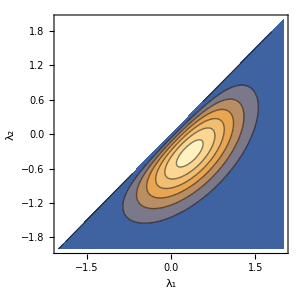

```mathematica
Block[{τ2=1},
ContourPlot[p12[λ1,λ2],{λ1,-2,2},{λ2,-2,λ1},PlotRange->All,FrameLabel->{"λ_1","λ_2"},ImageSize->300,Axes->True,AxesOrigin->{0,0}]
]
```

Distribution of the first eigenvalue

```mathematica
p1[λ1_]:=(ⅇ^(-(3 λ1^2)/(2 τ2^2)) (6 √(6/π) τ2+9 ⅇ^((3 λ1^2)/(8 τ2^2)) λ1 (1+Erf[(√(3/2) λ1)/(2 τ2)])))/(16 τ2^2)
p2[λ2_]:=(ⅇ^(-(3 λ2^2)/(2 τ2^2)) (6 √(6/π) τ2-9 ⅇ^((3 λ2^2)/(8 τ2^2)) λ2 Erfc[(√(3/2) λ2)/(2 τ2)]))/(16 τ2^2)
```

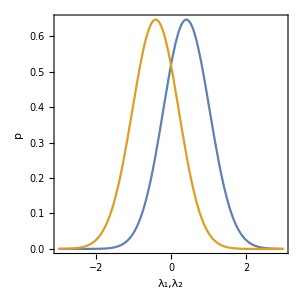

```mathematica
Block[{τ2=1},
Plot[{p1[x],p2[x]},{x,-3,3},Frame->True,FrameLabel->{"λ_1,λ_2","p"},ImageSize->300,AspectRatio->1]
]
```

```mathematica
A1[bp_]=FullSimplify[Integrate[p1[λ1],{λ1,1/bp,∞},Assumptions->{τ2>0}]]
A2[bp_]=FullSimplify[Integrate[p2[λ2],{λ2,1/bp,∞},Assumptions->{τ2>0}]]

Limit[A1[bp],bp->∞]
Limit[A2[bp],bp->∞]
```

1/4 (ⅇ^(-9/(8 bp^2 τ2^2)) (1+Erf[(√(3/2))/(2 bp τ2)])+2 Erfc[(√(3/2))/(bp τ2)])

-1/4 ⅇ^(-9/(8 bp^2 τ2^2)) Erfc[(√(3/2))/(2 bp τ2)]+1/2 Erfc[(√(3/2))/(bp τ2)]

3/4

1/4

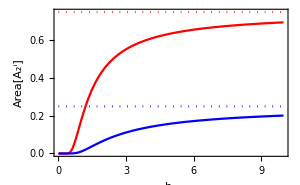

```mathematica
Block[{τ2=1},
Show[
Plot[{A1[bp],A2[bp]},{bp,0,10},PlotRange->All,PlotStyle->{Red,Blue}],
Plot[{3/4,1/4},{bp,0,10},PlotRange->All,PlotStyle->{{Dotted,Red},{Dotted,Blue}}],
Frame->True,FrameLabel->{"b_+","Area[A_2^i]"},ImageSize->300
]
]
```

## The cusp singularity in 2D

```mathematica
FullSimplify[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}})ᵀ.({{λ1, 0}, {0, λ2}}).({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}})]
```

{{λ1 Cos[ω]^2+λ2 Sin[ω]^2,(-λ1+λ2) Cos[ω] Sin[ω]},{(-λ1+λ2) Cos[ω] Sin[ω],λ2 Cos[ω]^2+λ1 Sin[ω]^2}}

```mathematica
FullSimplify[Eigensystem[{{λ1 Cos[ω]^2+λ2 Sin[ω]^2,(-λ1+λ2) Cos[ω] Sin[ω]},{(-λ1+λ2) Cos[ω] Sin[ω],λ2 Cos[ω]^2+λ1 Sin[ω]^2}}]]
```

{{λ1,λ2},{{-Cot[ω],1},{Tan[ω],1}}}

```mathematica
v1[x_,y_]:={Cos[ω[x,y]],-Sin[ω[x,y]]}
v2[x_,y_]:={Sin[ω[x,y]],Cos[ω[x,y]]}
```

```mathematica
T11[x_,y_]:=λ1 [x,y] Cos[ω[x,y]]^2+λ2[x,y] Sin[ω[x,y]]^2
T22[x_,y_]:=λ2[x,y] Cos[ω[x,y]]^2+λ1[x,y] Sin[ω[x,y]]^2
T12[x_,y_]:=(-λ1[x,y]+λ2[x,y]) Cos[ω[x,y]] Sin[ω[x,y]]
```

```mathematica
T11[x,y]
T12[x,y]
T22[x,y]
```

Sin[ω[x,y]]^2 λ2[x,y]+1/2 Cos[ω[x,y]]^2 (f^(0,2)[x,y]+f^(2,0)[x,y]+√(4 (f^(1,1)[x,y])^2+(-f^(0,2)[x,y]+f^(2,0)[x,y])^2))

Cos[ω[x,y]] Sin[ω[x,y]] (λ2[x,y]+1/2 (-f^(0,2)[x,y]-f^(2,0)[x,y]-√(4 (f^(1,1)[x,y])^2+(-f^(0,2)[x,y]+f^(2,0)[x,y])^2)))

Cos[ω[x,y]]^2 λ2[x,y]+1/2 Sin[ω[x,y]]^2 (f^(0,2)[x,y]+f^(2,0)[x,y]+√(4 (f^(1,1)[x,y])^2+(-f^(0,2)[x,y]+f^(2,0)[x,y])^2))

```mathematica
FullSimplify[Solve[
{t11==Cos[ω]^2 λ1+Sin[ω]^2 λ2,
(*t12==Cos[ω] Sin[ω] (-λ1+λ2),*)
t22==Sin[ω]^2 λ1+Cos[ω]^2 λ2},{λ1,λ2}]]
```

{{λ1→1/2 (t11+t22+(t11-t22) Sec[2 ω]),λ2→1/2 (t11+t22+(-t11+t22) Sec[2 ω])}}

```mathematica
FullSimplify[T11[x,y]/.ω[x,y]->0]
FullSimplify[T12[x,y]/.ω[x,y]->0]
FullSimplify[T22[x,y]/.ω[x,y]->0]
```

λ1[x,y]

0

λ2[x,y]

```mathematica
FullSimplify[D[D[λ1[x,y],{{x,y}}].v1[x,y],{{x,y}}]/.ω[x,y]->0]
```

{-λ1^(0,1)[x,y] ω^(1,0)[x,y]+λ1^(2,0)[x,y],-λ1^(0,1)[x,y] ω^(0,1)[x,y]+λ1^(1,1)[x,y]}

```mathematica
FullSimplify[D[T11[x,y],x]/.ω[x,y]->0]
FullSimplify[D[T11[x,y],y]/.ω[x,y]->0]
FullSimplify[D[T12[x,y],x]/.ω[x,y]->0]
FullSimplify[D[T12[x,y],y]/.ω[x,y]->0]
FullSimplify[D[T22[x,y],x]/.ω[x,y]->0]
FullSimplify[D[T22[x,y],y]/.ω[x,y]->0]
```

λ1^(1,0)[x,y]

λ1^(0,1)[x,y]

(-λ1[x,y]+λ2[x,y]) ω^(1,0)[x,y]

(-λ1[x,y]+λ2[x,y]) ω^(0,1)[x,y]

λ2^(1,0)[x,y]

λ2^(0,1)[x,y]

```mathematica
FullSimplify[D[T11[x,y],x,x]/.ω[x,y]->0]
FullSimplify[D[T11[x,y],x,y]/.ω[x,y]->0]
FullSimplify[D[T11[x,y],y,y]/.ω[x,y]->0]

FullSimplify[D[T12[x,y],x,x]/.ω[x,y]->0]
FullSimplify[D[T12[x,y],x,y]/.ω[x,y]->0]
FullSimplify[D[T12[x,y],y,y]/.ω[x,y]->0]

FullSimplify[D[T22[x,y],x,x]/.ω[x,y]->0]
FullSimplify[D[T22[x,y],x,y]/.ω[x,y]->0]
FullSimplify[D[T22[x,y],y,y]/.ω[x,y]->0]
```

2 (-λ1[x,y]+λ2[x,y]) (ω^(1,0)[x,y])^2+λ1^(2,0)[x,y]

2 (-λ1[x,y]+λ2[x,y]) ω^(0,1)[x,y] ω^(1,0)[x,y]+λ1^(1,1)[x,y]

2 (-λ1[x,y]+λ2[x,y]) (ω^(0,1)[x,y])^2+λ1^(0,2)[x,y]

2 (-λ1^(1,0)[x,y]+λ2^(1,0)[x,y]) ω^(1,0)[x,y]+(-λ1[x,y]+λ2[x,y]) ω^(2,0)[x,y]

ω^(0,1)[x,y] (-λ1^(1,0)[x,y]+λ2^(1,0)[x,y])+(-λ1^(0,1)[x,y]+λ2^(0,1)[x,y]) ω^(1,0)[x,y]+(-λ1[x,y]+λ2[x,y]) ω^(1,1)[x,y]

2 (-λ1^(0,1)[x,y]+λ2^(0,1)[x,y]) ω^(0,1)[x,y]+(-λ1[x,y]+λ2[x,y]) ω^(0,2)[x,y]

2 (λ1[x,y]-λ2[x,y]) (ω^(1,0)[x,y])^2+λ2^(2,0)[x,y]

2 (λ1[x,y]-λ2[x,y]) ω^(0,1)[x,y] ω^(1,0)[x,y]+λ2^(1,1)[x,y]

2 (λ1[x,y]-λ2[x,y]) (ω^(0,1)[x,y])^2+λ2^(0,2)[x,y]

```mathematica
FullSimplify[D[λ1[x,y],{{x,y}}].v1[x,y]/.ω[x,y]->0]
FullSimplify[D[λ2[x,y],{{x,y}}].v2[x,y]/.ω[x,y]->0]
FullSimplify[D[λ1[x,y],{{x,y}}].v1[x,y]/.ω[x,y]->0]
FullSimplify[D[λ2[x,y],{{x,y}}].v2[x,y]/.ω[x,y]->0]
```

λ1^(1,0)[x,y]

λ2^(0,1)[x,y]

λ1^(1,0)[x,y]

λ2^(0,1)[x,y]

```mathematica
FullSimplify[D[D[λ1[x,y],{{x,y}}].v1[x,y],{{x,y}}].v1[x,y]/.ω[x,y]->0]
FullSimplify[D[D[λ1[x,y],{{x,y}}].v1[x,y],{{x,y}}].v2[x,y]/.ω[x,y]->0]
FullSimplify[D[D[λ1[x,y],{{x,y}}].v2[x,y],{{x,y}}].v1[x,y]/.ω[x,y]->0]
FullSimplify[D[D[λ1[x,y],{{x,y}}].v2[x,y],{{x,y}}].v2[x,y]/.ω[x,y]->0]

FullSimplify[D[D[λ2[x,y],{{x,y}}].v1[x,y],{{x,y}}].v1[x,y]/.ω[x,y]->0]
FullSimplify[D[D[λ2[x,y],{{x,y}}].v1[x,y],{{x,y}}].v2[x,y]/.ω[x,y]->0]
FullSimplify[D[D[λ2[x,y],{{x,y}}].v2[x,y],{{x,y}}].v1[x,y]/.ω[x,y]->0]
FullSimplify[D[D[λ2[x,y],{{x,y}}].v2[x,y],{{x,y}}].v2[x,y]/.ω[x,y]->0]
```

-λ1^(0,1)[x,y] ω^(1,0)[x,y]+λ1^(2,0)[x,y]

-λ1^(0,1)[x,y] ω^(0,1)[x,y]+λ1^(1,1)[x,y]

λ1^(1,0)[x,y] ω^(1,0)[x,y]+λ1^(1,1)[x,y]

λ1^(0,2)[x,y]+ω^(0,1)[x,y] λ1^(1,0)[x,y]

-λ2^(0,1)[x,y] ω^(1,0)[x,y]+λ2^(2,0)[x,y]

-λ2^(0,1)[x,y] ω^(0,1)[x,y]+λ2^(1,1)[x,y]

λ2^(1,0)[x,y] ω^(1,0)[x,y]+λ2^(1,1)[x,y]

λ2^(0,2)[x,y]+ω^(0,1)[x,y] λ2^(1,0)[x,y]

### Alternative

```mathematica
f[x_,y_]:=1/2(T11 x^2+(*2T12 x y+*) T22 y^2)+1/(3!)(T111 x^3+3 T112 x^2 y+3T122 x y^2+T222 y^3)+1/(4!)(T1111 x^4+4T1112 x^3 y+6T1122 x^2 y^2+4T1222 x y^3+T2222 y^4)
```

```mathematica
{D[f[x,y],x,x],D[f[x,y],x,y],D[f[x,y],y,y]}/.{x->0,y->0}
{D[f[x,y],x,x,x],D[f[x,y],x,x,y],D[f[x,y],x,y,y],D[f[x,y],y,y,y]}/.{x->0,y->0}
{D[f[x,y],x,x,x,x],D[f[x,y],x,x,x,y],D[f[x,y],x,x,y,y],D[f[x,y],x,y,y,y],D[f[x,y],y,y,y,y]}/.{x->0,y->0}
```

{T11,0,T22}

{T111,T112,T122,T222}

{T1111,T1112,T1122,T1222,T2222}

```mathematica
({{λ2[x_,y_], λ1[x_,y_]}, {w2[x_,y_], w1[x_,y_]}})=Eigensystem[D[D[f[x,y],{{x,y}}],{{x,y}}]]
```

{{1/4 (2 T11+2 T22+2 T111 x+2 T122 x+T1111 x^2+T1122 x^2+2 T112 y+2 T222 y+2 T1112 x y+2 T1222 x y+T1122 y^2+T2222 y^2-√((-2 T11-2 T22-2 T111 x-2 T122 x-T1111 x^2-T1122 x^2-2 T112 y-2 T222 y-2 T1112 x y-2 T1222 x y-T1122 y^2-T2222 y^2)^2-4 (4 T11 T22+4 T11 T122 x+4 T111 T22 x-4 T112^2 x^2+2 T11 T1122 x^2+4 T111 T122 x^2+2 T1111 T22 x^2-4 T1112 T112 x^3+2 T111 T1122 x^3+2 T1111 T122 x^3-T1112^2 x^4+T1111 T1122 x^4+4 T112 T22 y+4 T11 T222 y-4 T112 T122 x y+4 T11 T1222 x y+4 T1112 T22 x y+4 T111 T222 x y-6 T112 T1122 x^2 y+4 T111 T1222 x^2 y+2 T1111 T222 x^2 y-2 T1112 T1122 x^3 y+2 T1111 T1222 x^3 y-4 T122^2 y^2+2 T1122 T22 y^2+4 T112 T222 y^2+2 T11 T2222 y^2-6 T1122 T122 x y^2+4 T1112 T222 x y^2+2 T111 T2222 x y^2-3 T1122^2 x^2 y^2+2 T1112 T1222 x^2 y^2+T1111 T2222 x^2 y^2-4 T122 T1222 y^3+2 T1122 T222 y^3+2 T112 T2222 y^3-2 T1122 T1222 x y^3+2 T1112 T2222 x y^3-T1222^2 y^4+T1122 T2222 y^4))),1/4 (2 T11+2 T22+2 T111 x+2 T122 x+T1111 x^2+T1122 x^2+2 T112 y+2 T222 y+2 T1112 x y+2 T1222 x y+T1122 y^2+T2222 y^2+√((-2 T11-2 T22-2 T111 x-2 T122 x-T1111 x^2-T1122 x^2-2 T112 y-2 T222 y-2 T1112 x y-2 T1222 x y-T1122 y^2-T2222 y^2)^2-4 (4 T11 T22+4 T11 T122 x+4 T111 T22 x-4 T112^2 x^2+2 T11 T1122 x^2+4 T111 T122 x^2+2 T1111 T22 x^2-4 T1112 T112 x^3+2 T111 T1122 x^3+2 T1111 T122 x^3-T1112^2 x^4+T1111 T1122 x^4+4 T112 T22 y+4 T11 T222 y-4 T112 T122 x y+4 T11 T1222 x y+4 T1112 T22 x y+4 T111 T222 x y-6 T112 T1122 x^2 y+4 T111 T1222 x^2 y+2 T1111 T222 x^2 y-2 T1112 T1122 x^3 y+2 T1111 T1222 x^3 y-4 T122^2 y^2+2 T1122 T22 y^2+4 T112 T222 y^2+2 T11 T2222 y^2-6 T1122 T122 x y^2+4 T1112 T222 x y^2+2 T111 T2222 x y^2-3 T1122^2 x^2 y^2+2 T1112 T1222 x^2 y^2+T1111 T2222 x^2 y^2-4 T122 T1222 y^3+2 T1122 T222 y^3+2 T112 T2222 y^3-2 T1122 T1222 x y^3+2 T1112 T2222 x y^3-T1222^2 y^4+T1122 T2222 y^4)))},{{-((-2 T11+2 T22-2 T111 x+2 T122 x-T1111 x^2+T1122 x^2-2 T112 y+2 T222 y-2 T1112 x y+2 T1222 x y-T1122 y^2+T2222 y^2+√(4 T11^2-8 T11 T22+4 T22^2+8 T11 T111 x-8 T11 T122 x-8 T111 T22 x+8 T122 T22 x+4 T111^2 x^2+4 T11 T1111 x^2+16 T112^2 x^2-4 T11 T1122 x^2-8 T111 T122 x^2+4 T122^2 x^2-4 T1111 T22 x^2+4 T1122 T22 x^2+4 T111 T1111 x^3+16 T1112 T112 x^3-4 T111 T1122 x^3-4 T1111 T122 x^3+4 T1122 T122 x^3+T1111^2 x^4+4 T1112^2 x^4-2 T1111 T1122 x^4+T1122^2 x^4+8 T11 T112 y-8 T112 T22 y-8 T11 T222 y+8 T22 T222 y+8 T11 T1112 x y+8 T111 T112 x y+24 T112 T122 x y-8 T11 T1222 x y-8 T1112 T22 x y+8 T1222 T22 x y-8 T111 T222 x y+8 T122 T222 x y+8 T111 T1112 x^2 y+4 T1111 T112 x^2 y+28 T112 T1122 x^2 y+8 T1112 T122 x^2 y-8 T111 T1222 x^2 y+8 T122 T1222 x^2 y-4 T1111 T222 x^2 y+4 T1122 T222 x^2 y+4 T1111 T1112 x^3 y+12 T1112 T1122 x^3 y-4 T1111 T1222 x^3 y+4 T1122 T1222 x^3 y+4 T112^2 y^2+4 T11 T1122 y^2+16 T122^2 y^2-4 T1122 T22 y^2-8 T112 T222 y^2+4 T222^2 y^2-4 T11 T2222 y^2+4 T22 T2222 y^2+8 T1112 T112 x y^2+4 T111 T1122 x y^2+28 T1122 T122 x y^2+8 T112 T1222 x y^2-8 T1112 T222 x y^2+8 T1222 T222 x y^2-4 T111 T2222 x y^2+4 T122 T2222 x y^2+4 T1112^2 x^2 y^2+2 T1111 T1122 x^2 y^2+14 T1122^2 x^2 y^2+4 T1222^2 x^2 y^2-2 T1111 T2222 x^2 y^2+2 T1122 T2222 x^2 y^2+4 T112 T1122 y^3+16 T122 T1222 y^3-4 T1122 T222 y^3-4 T112 T2222 y^3+4 T222 T2222 y^3+4 T1112 T1122 x y^3+12 T1122 T1222 x y^3-4 T1112 T2222 x y^3+4 T1222 T2222 x y^3+T1122^2 y^4+4 T1222^2 y^4-2 T1122 T2222 y^4+T2222^2 y^4))/(2 (2 T112 x+T1112 x^2+2 T122 y+2 T1122 x y+T1222 y^2))),1},{-((-2 T11+2 T22-2 T111 x+2 T122 x-T1111 x^2+T1122 x^2-2 T112 y+2 T222 y-2 T1112 x y+2 T1222 x y-T1122 y^2+T2222 y^2-√(4 T11^2-8 T11 T22+4 T22^2+8 T11 T111 x-8 T11 T122 x-8 T111 T22 x+8 T122 T22 x+4 T111^2 x^2+4 T11 T1111 x^2+16 T112^2 x^2-4 T11 T1122 x^2-8 T111 T122 x^2+4 T122^2 x^2-4 T1111 T22 x^2+4 T1122 T22 x^2+4 T111 T1111 x^3+16 T1112 T112 x^3-4 T111 T1122 x^3-4 T1111 T122 x^3+4 T1122 T122 x^3+T1111^2 x^4+4 T1112^2 x^4-2 T1111 T1122 x^4+T1122^2 x^4+8 T11 T112 y-8 T112 T22 y-8 T11 T222 y+8 T22 T222 y+8 T11 T1112 x y+8 T111 T112 x y+24 T112 T122 x y-8 T11 T1222 x y-8 T1112 T22 x y+8 T1222 T22 x y-8 T111 T222 x y+8 T122 T222 x y+8 T111 T1112 x^2 y+4 T1111 T112 x^2 y+28 T112 T1122 x^2 y+8 T1112 T122 x^2 y-8 T111 T1222 x^2 y+8 T122 T1222 x^2 y-4 T1111 T222 x^2 y+4 T1122 T222 x^2 y+4 T1111 T1112 x^3 y+12 T1112 T1122 x^3 y-4 T1111 T1222 x^3 y+4 T1122 T1222 x^3 y+4 T112^2 y^2+4 T11 T1122 y^2+16 T122^2 y^2-4 T1122 T22 y^2-8 T112 T222 y^2+4 T222^2 y^2-4 T11 T2222 y^2+4 T22 T2222 y^2+8 T1112 T112 x y^2+4 T111 T1122 x y^2+28 T1122 T122 x y^2+8 T112 T1222 x y^2-8 T1112 T222 x y^2+8 T1222 T222 x y^2-4 T111 T2222 x y^2+4 T122 T2222 x y^2+4 T1112^2 x^2 y^2+2 T1111 T1122 x^2 y^2+14 T1122^2 x^2 y^2+4 T1222^2 x^2 y^2-2 T1111 T2222 x^2 y^2+2 T1122 T2222 x^2 y^2+4 T112 T1122 y^3+16 T122 T1222 y^3-4 T1122 T222 y^3-4 T112 T2222 y^3+4 T222 T2222 y^3+4 T1112 T1122 x y^3+12 T1122 T1222 x y^3-4 T1112 T2222 x y^3+4 T1222 T2222 x y^3+T1122^2 y^4+4 T1222^2 y^4-2 T1122 T2222 y^4+T2222^2 y^4))/(2 (2 T112 x+T1112 x^2+2 T122 y+2 T1122 x y+T1222 y^2))),1}}}

```mathematica
FullSimplify[Limit[λ1[x,y],{T12->0,x->0}]/.y->0,Assumptions->{T11>T22}]
FullSimplify[Limit[λ2[x,y],{T12->0,x->0}]/.y->0,Assumptions->{T11>T22}]
```

T11

T22

```mathematica
FullSimplify[D[λ1[x,y],{{x,y}}]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
FullSimplify[D[λ2[x,y],{{x,y}}]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
```

{T111,T112}

{T122,T222}

```mathematica
FullSimplify[D[λ1[x,y],x,x]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
FullSimplify[D[λ1[x,y],x,y]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
FullSimplify[D[λ1[x,y],y,y]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]

FullSimplify[D[λ2[x,y],x,x]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
FullSimplify[D[λ2[x,y],x,y]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
FullSimplify[D[λ2[x,y],y,y]/.{x->0,y->0,T12->0},Assumptions->{T11>T22}]
```

T1111+(2 T112^2)/(T11-T22)

T1112+(2 T112 T122)/(T11-T22)

T1122+(2 T122^2)/(T11-T22)

T1122+(2 T112^2)/(-T11+T22)

T1222+(2 T112 T122)/(-T11+T22)

(2 T122^2)/(-T11+T22)+T2222

## Eigenvalues in terms of derivatives

```mathematica
λ1[x_,y_]:=1/2(D[f[x,y],x,x]+D[f[x,y],y,y] +√(4 D[f[x,y],x,y]^2+(D[f[x,y],x,x]-D[f[x,y],y,y])^2))
```

```mathematica
FullSimplify[λ1[x,y]/.{
Derivative[2,0][f][x,y]->T11,
Derivative[1,1][f][x,y]->T12,
Derivative[0,2][f][x,y]->T22,

Derivative[3,0][f][x,y]->T111,
Derivative[2,1][f][x,y]->T112,
Derivative[1,2][f][x,y]->T122,
Derivative[0,3][f][x,y]->T222,

Derivative[4,0][f][x,y]->T1111,
Derivative[3,1][f][x,y]->T1112,
Derivative[2,2][f][x,y]->T1122,
Derivative[1,3][f][x,y]->T1222,
Derivative[0,4][f][x,y]->T2222},Assumptions->{T11>T22}]
```

1/2 (T11+√(4 T12^2+(T11-T22)^2)+T22)

```mathematica
FullSimplify[D[λ1[x,y],{{x,y}}]/.{
Derivative[2,0][f][x,y]->T11,
Derivative[1,1][f][x,y]->T12,
Derivative[0,2][f][x,y]->T22,

Derivative[3,0][f][x,y]->T111,
Derivative[2,1][f][x,y]->T112,
Derivative[1,2][f][x,y]->T122,
Derivative[0,3][f][x,y]->T222,

Derivative[4,0][f][x,y]->T1111,
Derivative[3,1][f][x,y]->T1112,
Derivative[2,2][f][x,y]->T1122,
Derivative[1,3][f][x,y]->T1222,
Derivative[0,4][f][x,y]->T2222},Assumptions->{T11>T22}]
```

{1/2 (T111+T122+(4 T112 T12+(T111-T122) (T11-T22))/(√(4 T12^2+(T11-T22)^2))),1/2 (T112+(4 T12 T122+(T11-T22) (T112-T222))/(√(4 T12^2+(T11-T22)^2))+T222)}

```mathematica
FullSimplify[D[D[λ1[x,y],{{x,y}}],{{x,y}}]/.{
Derivative[2,0][f][x,y]->T11,
Derivative[1,1][f][x,y]->T12,
Derivative[0,2][f][x,y]->T22,

Derivative[3,0][f][x,y]->T111,
Derivative[2,1][f][x,y]->T112,
Derivative[1,2][f][x,y]->T122,
Derivative[0,3][f][x,y]->T222,

Derivative[4,0][f][x,y]->T1111,
Derivative[3,1][f][x,y]->T1112,
Derivative[2,2][f][x,y]->T1122,
Derivative[1,3][f][x,y]->T1222,
Derivative[0,4][f][x,y]->T2222},Assumptions->{T11>T22}]
```

{{1/2 (T1111+T1122-(4 T112 T12+(T111-T122) (T11-T22))^2/((4 T12^2+(T11-T22)^2)^(3/2))+(4 T112^2+4 T1112 T12+(T111-T122)^2+(T1111-T1122) (T11-T22))/(√(4 T12^2+(T11-T22)^2))),1/2 (T1112+T1222-((4 T112 T12+(T111-T122) (T11-T22)) (4 T12 T122+(T11-T22) (T112-T222)))/((4 T12^2+(T11-T22)^2)^(3/2))+(4 T1122 T12+(T1112-T1222) (T11-T22)+T111 (T112-T222)+T122 (3 T112+T222))/(√(4 T12^2+(T11-T22)^2)))},{1/2 (T1112+T1222-((4 T112 T12+(T111-T122) (T11-T22)) (4 T12 T122+(T11-T22) (T112-T222)))/((4 T12^2+(T11-T22)^2)^(3/2))+(4 T1122 T12+(T1112-T1222) (T11-T22)+T111 (T112-T222)+T122 (3 T112+T222))/(√(4 T12^2+(T11-T22)^2))),1/2 (T1122-(4 T12 T122+(T11-T22) (T112-T222))^2/((4 T12^2+(T11-T22)^2)^(3/2))+(4 T122^2+4 T12 T1222+(T112-T222)^2+(T11-T22) (T1122-T2222))/(√(4 T12^2+(T11-T22)^2))+T2222)}}

## Non-linear eigenvalue relations

```mathematica
rep={
Derivative[2,0][f][x,y]->T11,
Derivative[1,1][f][x,y]->T12,
Derivative[0,2][f][x,y]->T22,

Derivative[3,0][f][x,y]->T111,
Derivative[2,1][f][x,y]->T112,
Derivative[1,2][f][x,y]->T122,
Derivative[0,3][f][x,y]->T222,

Derivative[4,0][f][x,y]->T1111,
Derivative[3,1][f][x,y]->T1112,
Derivative[2,2][f][x,y]->T1122,
Derivative[1,3][f][x,y]->T1222,
Derivative[0,4][f][x,y]->T2222,

Derivative[5,0][f][x,y]->T11111,
Derivative[4,1][f][x,y]->T11112,
Derivative[3,2][f][x,y]->T11122,
Derivative[2,3][f][x,y]->T11222,
Derivative[1,4][f][x,y]->T12222,
Derivative[0,5][f][x,y]->T22222};
```

```mathematica
FullSimplify[D[D[f[x Cos[ω]-y Sin[ω],x Sin[ω]+y Cos[ω]],{{x,y}}],{{x,y}}]]
```

{{Sin[ω]^2 f^(0,2)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]+Sin[2 ω] f^(1,1)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]+Cos[ω]^2 f^(2,0)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]],Cos[2 ω] f^(1,1)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]+Cos[ω] Sin[ω] (f^(0,2)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]-f^(2,0)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]])},{Cos[2 ω] f^(1,1)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]+Cos[ω] Sin[ω] (f^(0,2)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]-f^(2,0)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]),Cos[ω]^2 f^(0,2)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]+Sin[ω] (-2 Cos[ω] f^(1,1)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]+Sin[ω] f^(2,0)[x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]])}}

```mathematica
FullSimplify[D[f[x Cos[ω]-y Sin[ω],x Sin[ω]+y Cos[ω]],x,x]/.{Derivative[2,0][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T11,
Derivative[1,1][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T12,
Derivative[0,2][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T22}]
FullSimplify[D[f[x Cos[ω]-y Sin[ω],x Sin[ω]+y Cos[ω]],x,y]/.{Derivative[2,0][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T11,
Derivative[1,1][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T12,
Derivative[0,2][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T22}]
FullSimplify[D[f[x Cos[ω]-y Sin[ω],x Sin[ω]+y Cos[ω]],y,y]/.{Derivative[2,0][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T11,
Derivative[1,1][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T12,
Derivative[0,2][f][x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]]->T22}]
```

T11 Cos[ω]^2+T22 Sin[ω]^2+T12 Sin[2 ω]

T12 Cos[2 ω]+(-T11+T22) Cos[ω] Sin[ω]

T22 Cos[ω]^2-2 T12 Cos[ω] Sin[ω]+T11 Sin[ω]^2

```mathematica
FullSimplify[D[f[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}}).{x,y}],x]/.{Derivative[{1,0}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T1,
Derivative[{0,1}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T2}]
FullSimplify[D[f[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}}).{x,y}],y]/.{Derivative[{1,0}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T1,
Derivative[{0,1}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T2}]
```

T1 Cos[ω]+T2 Sin[ω]

T2 Cos[ω]-T1 Sin[ω]

```mathematica
FullSimplify[D[f[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}}).{x,y}],x,x]/.{Derivative[{2,0}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T11,
Derivative[{1,1}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T12,
Derivative[{0,2}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T22}]
FullSimplify[D[f[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}}).{x,y}],x,y]/.{Derivative[{2,0}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T11,
Derivative[{1,1}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T12,
Derivative[{0,2}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T22}]
FullSimplify[D[f[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}}).{x,y}],y,y]/.{Derivative[{2,0}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T11,
Derivative[{1,1}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T12,
Derivative[{0,2}][f][{x Cos[ω]-y Sin[ω],y Cos[ω]+x Sin[ω]}]->T22}]
```

T11 Cos[ω]^2+T22 Sin[ω]^2+T12 Sin[2 ω]

T12 Cos[2 ω]+(-T11+T22) Cos[ω] Sin[ω]

T22 Cos[ω]^2-2 T12 Cos[ω] Sin[ω]+T11 Sin[ω]^2

```mathematica
FullSimplify[({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}})ᵀ.({{T11, T12}, {T12, T22}}).({{Cos[ω], -Sin[ω]}, {Sin[ω], Cos[ω]}})]
```

{{T11 Cos[ω]^2+T22 Sin[ω]^2+T12 Sin[2 ω],T12 Cos[2 ω]+(-T11+T22) Cos[ω] Sin[ω]},{T12 Cos[2 ω]+(-T11+T22) Cos[ω] Sin[ω],T22 Cos[ω]^2-2 T12 Cos[ω] Sin[ω]+T11 Sin[ω]^2}}

```mathematica
FullSimplify[Solve[{T12 Cos[2 ω]+1/2(-T11+T22) Sin[2ω]==0},ω]]
```

{{ω→ConditionalExpression[π C[1]-1/2 ⅈ Log[(T11+2 ⅈ T12-T22)/(√(4 T12^2+(T11-T22)^2))], C[1]∈ℤ]},{ω→ConditionalExpression[π C[1]-1/2 ⅈ Log[(-T11-2 ⅈ T12+T22)/(√(4 T12^2+(T11-T22)^2))], C[1]∈ℤ]}}

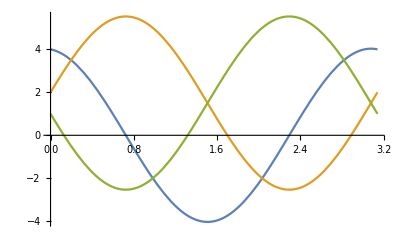

```mathematica
Module[{T12=4,T11=2,T22=1},
Plot[{T12 Cos[2 ω]+1/2(-T11+T22) Sin[2ω],T11 Cos[ω]^2+T22 Sin[ω]^2+T12 Sin[2 ω],T22 Cos[ω]^2-2 T12 Cos[ω] Sin[ω]+T11 Sin[ω]^2},{ω,0,π}]
]
```

```mathematica
λ1[x_,y_]:=1/2(D[f[x,y],x,x]+D[f[x,y],y,y] +√(4 D[f[x,y],x,y]^2+(D[f[x,y],x,x]-D[f[x,y],y,y])^2))
v1[x_,y_]:={(√(Derivative[2,0][f][x,y]+√(4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)-Derivative[0,2][f][x,y]))/(√2 (4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)^(1/4)),(√2 Derivative[1,1][f][x,y])/((4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)^(1/4) √(Derivative[2,0][f][x,y]+√(4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)-Derivative[0,2][f][x,y]))}

λ2[x_,y_]:=1/2(D[f[x,y],x,x]+D[f[x,y],y,y] -√(4 D[f[x,y],x,y]^2+(D[f[x,y],x,x]-D[f[x,y],y,y])^2))
v2[x_,y_]:={-(√2 Derivative[1,1][f][x,y])/((4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)^(1/4) √(Derivative[2,0][f][x,y]+√(4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)-Derivative[0,2][f][x,y])),(√(Derivative[2,0][f][x,y]+√(4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)-Derivative[0,2][f][x,y]))/(√2 (4 (Derivative[1,1][f][x,y])^2+(Derivative[2,0][f][x,y]-Derivative[0,2][f][x,y])^2)^(1/4))}
```

### First eigenvalue fields

```mathematica
FullSimplify[FullSimplify[λ1[x,y]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
```

T11

```mathematica
FullSimplify[FullSimplify[D[λ1[x,y],{{x,y}}]/.rep]/.T12->0,Assumptions->{T11>T22}]
```

{T111,T112}

```mathematica
FullSimplify[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]/.rep/.T12->0,Assumptions->{T11>T22}]

FullSimplify[D[v2[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]/.rep/.T12->0,Assumptions->{T11>T22}]
```

{T1111+(3 T112^2)/(T11-T22),T1112+(3 T112 T122)/(T11-T22)}

{T1112+(T112 (T111-2 T122))/(-T11+T22),T1122+((T111-2 T122) T122)/(-T11+T22)}

```mathematica
FullSimplify[D[v1[x,y].D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}],{{x,y}}]/.rep/.T12->0,Assumptions->{T11>T22}]
```

{T11111+(T112 (-9 T111 T112+15 T112 T122+10 T1112 (T11-T22)))/(T11-T22)^2,1/(T11-T22)^2(T11^2 T11112-3 T112^3+T11 (6 T112 T1122+4 T1112 T122-2 T11112 T22)+T22 (-4 T1112 T122+T11112 T22)-6 T112 ((T111-2 T122) T122+T1122 T22)+3 T112^2 T222)}

#### A3 points

```mathematica
perp[{a_,b_}]:={-b,a}
```

```mathematica
FullSimplify[
perp[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]].D[λ1[x,y],{{x,y}}]
/.rep/.T12->0,Assumptions->{T11>T22}]
FullSimplify[
perp[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]].D[λ1[x,y],{{x,y}}]
/.rep/.T12->0/.T111->0,Assumptions->{T11>T22}]
```

-T111 T1112+T1111 T112+(3 T112 (T112^2-T111 T122))/(T11-T22)

T1111 T112+(3 T112^3)/(T11-T22)

```mathematica
FullSimplify[
Det[FullSimplify[
{D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}],D[perp[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]].D[λ1[x,y],{{x,y}}],{{x,y}}]}
/.rep/.T12->0,Assumptions->{T11>T22}]]/.{T111->0,T1111->-(3 T112^2)/(T11-T22)}
]
FullSimplify[
Det[FullSimplify[
{D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}],D[perp[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]].D[λ1[x,y],{{x,y}}],{{x,y}}]}
/.rep/.T12->0,Assumptions->{T11>T22}]]/.{T111->0,T112->0}
]
```

-1/(T11-T22)^3 T112 (T11 T1112+3 T112 T122-T1112 T22) (T11^2 T11111+10 T11 T1112 T112+15 T112^2 T122-2 (T11 T11111+5 T1112 T112) T22+T11111 T22^2)

T1111 (-T1112^2+T1111 (T1122+(2 T122^2)/(T11-T22)))

```mathematica
FullSimplify[
Det[FullSimplify[
{D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}],D[perp[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]].D[λ1[x,y],{{x,y}}],{{x,y}}]}
/.rep/.T12->0,Assumptions->{T11>T22}]]/.{T111->0,T1111->-(3 T112^2)/(T11-T22)}
]

FullSimplify[
Det[FullSimplify[
{D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}],D[perp[D[v1[x,y].D[λ1[x,y],{{x,y}}],{{x,y}}]].D[λ1[x,y],{{x,y}}],{{x,y}}]}
/.rep/.T12->0,Assumptions->{T11>T22}]]/.{T111->0,T112->0}
]
```

-1/(T11-T22)^3 T112 (T11 T1112+3 T112 T122-T1112 T22) (T11^2 T11111+10 T11 T1112 T112+15 T112^2 T122-2 (T11 T11111+5 T1112 T112) T22+T11111 T22^2)

T1111 (-T1112^2+T1111 (T1122+(2 T122^2)/(T11-T22)))

```mathematica
FullSimplify[Integrate[DiracDelta[T112(T1111+(3 T112^2)/(λ-T22))]f[T1111],{T1111,-∞,∞}],Assumptions->{T112∈Reals,λ>T22}]
```

f[(3 T112^2)/(T22-λ)]/Abs[T112]

### Second eigenvalue fields

```mathematica
FullSimplify[FullSimplify[λ2[x,y]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
```

T22

```mathematica
FullSimplify[FullSimplify[D[λ2[x,y],{{x,y}}]/.rep]/.T12->0,Assumptions->{T11>T22}]
```

{T122,T222}

```mathematica
FullSimplify[D[v1[x,y].D[λ2[x,y],{{x,y}}],{{x,y}}]/.rep/.T12->0,Assumptions->{T11>T22}]

FullSimplify[D[v2[x,y].D[λ2[x,y],{{x,y}}],{{x,y}}]/.rep/.T12->0,Assumptions->{T11>T22}]
```

{T1122+(T112 (-2 T112+T222))/(T11-T22),(-2 T112 T122+T11 T1222-T1222 T22+T122 T222)/(T11-T22)}

{T1222+(3 T112 T122)/(-T11+T22),(3 T122^2)/(-T11+T22)+T2222}

```mathematica
FullSimplify[D[v2[x,y].D[v2[x,y].D[λ2[x,y],{{x,y}}],{{x,y}}],{{x,y}}]/.rep/.T12->0,Assumptions->{T11>T22}]
```

{1/(T11-T22)^2(12 T112^2 T122+3 (T111-T122) T122^2+T11^2 T12222+6 T1122 T122 T22+T12222 T22^2-2 T11 (3 T1122 T122+T12222 T22)+T112 (-4 T11 T1222+4 T1222 T22-6 T122 T222)),(T122 (15 T112 T122+10 T1222 (-T11+T22)-9 T122 T222))/(T11-T22)^2+T22222}

### Eigenvalue fields

```mathematica
FullSimplify[FullSimplify[D[λ1[x,y],x,x]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
FullSimplify[FullSimplify[D[λ1[x,y],x,y]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
FullSimplify[FullSimplify[D[λ1[x,y],y,y]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]

FullSimplify[FullSimplify[D[λ2[x,y],x,x]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
FullSimplify[FullSimplify[D[λ2[x,y],x,y]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
FullSimplify[FullSimplify[D[λ2[x,y],y,y]/.rep]/.T12->0,Assumptions->{T11>T22>0,ν∈Reals}]
```

T1111+(2 T112^2)/(T11-T22)

T1112+(2 T112 T122)/(T11-T22)

T1122+(2 T122^2)/(T11-T22)

T1122+(2 T112^2)/(-T11+T22)

T1222+(2 T112 T122)/(-T11+T22)

(2 T122^2)/(-T11+T22)+T2222

### Scale space

```mathematica
nabla[f_]:=D[f,x,x]+D[f,y,y]
```

```mathematica
λ1R[x_,y_]:=R/2(D[nabla[f[x,y]],x,x]+D[nabla[f[x,y]],y,y] +(4D[f[x,y],x,y]nabla[D[f[x,y],x,y]]+(D[f[x,y],x,x]-D[f[x,y],y,y])(nabla[D[f[x,y],x,x]]-nabla[D[f[x,y],y,y]]))/(√(4 D[f[x,y],x,y]^2+(D[f[x,y],x,x]-D[f[x,y],y,y])^2)))
```

```mathematica
H[x_,y_]=Simplify[D[λ1[x,y],x,x]D[λ1[x,y],y,y]-D[λ1[x,y],x,y]^2];
```

```mathematica
FullSimplify[H[x,y]/.rep/.T12->0,Assumptions->{T11>T22}]
```

-T1112^2+T1111 T1122+(2 (T112^2 T1122-2 T1112 T112 T122+T1111 T122^2))/(T11-T22)

```mathematica
Beep[]
```

```mathematica
s[f_]:=Simplify[f/.rep/.T12->0,Assumptions->T11>T22]
```

```mathematica
FullSimplify[-s[D[λ1R[x,y],x]](s[D[H[x,y],x]]s[ D[λ1[x,y],y,y]]-s[D[H[x,y],y]]s[ D[λ1[x,y],x,y]])+s[D[λ1R[x,y],y]](s[D[H[x,y],x]]s[ D[λ1[x,y],x,y]]-s[D[H[x,y],y]] s[D[λ1[x,y],x,x]])
,Assumptions->T11>T22]
```

1/(8 (T11-T22)^5)R ((2 T122 (T1112+T1222)+(T11112+T11222) (T11-T22)) (8 (T11-T22) (T11 T1111+2 T112^2-T1111 T22) (2 T112^3 T1122+T11^2 (2 T1112 T11122-T11112 T1122-T1111 T11222)-4 T111 T1112 T122^2-6 T1112 T1122 T122 T22+2 T11112 T122^2 T22+6 T1111 T122 T1222 T22+2 T1112 T11122 T22^2-T11112 T1122 T22^2-T1111 T11222 T22^2+2 T11 (-T112^2 T11222-T122 (-3 T1112 T1122+T11112 T122+3 T1111 T1222)+2 T112 (-T1122^2+T11122 T122+T1112 T1222)+(-2 T1112 T11122+T11112 T1122+T1111 T11222) T22)-6 T1111 T122^2 T222-2 T112^2 (4 T1112 T122+2 T122 T1222-T11222 T22+T1122 T222)+T112 (4 T111 T1122 T122+6 T1111 T122^2+4 T1122 T122^2+4 T1122^2 T22-4 T11122 T122 T22-4 T1112 T1222 T22+8 T1112 T122 T222))+(T11 T1112+2 T112 T122-T1112 T22) (8 (T11 T1122+2 T122^2-T1122 T22) (T11^2 T11111+6 T112^2 (-T111+T122)-6 T1112 T112 T22+T11111 T22^2+T11 (6 T1112 T112-2 T11111 T22))-8 (2 T11 T1112+4 T112 T122-2 T1112 T22) (T11^2 T11112-2 T112^3+2 T11 (2 T112 T1122+T1112 T122-T11112 T22)+T22 (-2 T1112 T122+T11112 T22)-4 T112 ((T111-T122) T122+T1122 T22)+2 T112^2 T222)+8 (T11 T1111+2 T112^2-T1111 T22) (T11^2 T11122-4 T112^2 T122-2 T111 T122^2+2 T122^3-4 T1122 T122 T22-2 T112 T1222 T22+T11122 T22^2+2 T11 (2 T1122 T122+T112 T1222-T11122 T22)+4 T112 T122 T222)))-(2 T112 (T1112+T1222)+(T11111+T11122) (T11-T22)) (8 (T11-T22) (T11 T1112+2 T112 T122-T1112 T22) (2 T112^3 T1122+T11^2 (2 T1112 T11122-T11112 T1122-T1111 T11222)-4 T111 T1112 T122^2-6 T1112 T1122 T122 T22+2 T11112 T122^2 T22+6 T1111 T122 T1222 T22+2 T1112 T11122 T22^2-T11112 T1122 T22^2-T1111 T11222 T22^2+2 T11 (-T112^2 T11222-T122 (-3 T1112 T1122+T11112 T122+3 T1111 T1222)+2 T112 (-T1122^2+T11122 T122+T1112 T1222)+(-2 T1112 T11122+T11112 T1122+T1111 T11222) T22)-6 T1111 T122^2 T222-2 T112^2 (4 T1112 T122+2 T122 T1222-T11222 T22+T1122 T222)+T112 (4 T111 T1122 T122+6 T1111 T122^2+4 T1122 T122^2+4 T1122^2 T22-4 T11122 T122 T22-4 T1112 T1222 T22+8 T1112 T122 T222))+(T11 T1122+2 T122^2-T1122 T22) (8 (T11 T1122+2 T122^2-T1122 T22) (T11^2 T11111+6 T112^2 (-T111+T122)-6 T1112 T112 T22+T11111 T22^2+T11 (6 T1112 T112-2 T11111 T22))-8 (2 T11 T1112+4 T112 T122-2 T1112 T22) (T11^2 T11112-2 T112^3+2 T11 (2 T112 T1122+T1112 T122-T11112 T22)+T22 (-2 T1112 T122+T11112 T22)-4 T112 ((T111-T122) T122+T1122 T22)+2 T112^2 T222)+8 (T11 T1111+2 T112^2-T1111 T22) (T11^2 T11122-4 T112^2 T122-2 T111 T122^2+2 T122^3-4 T1122 T122 T22-2 T112 T1222 T22+T11122 T22^2+2 T11 (2 T1122 T122+T112 T1222-T11122 T22)+4 T112 T122 T222))))

```mathematica
Integrate[DiracDelta[-T1112^2+T1111 T1122+(2 (T112^2 T1122-2 T1112 T112 T122+T1111 T122^2))/(T11-T22)]f[T1111],{T1111,-∞,∞}]
```

(Boole[-∞<(-2 T112^2 T1122+T1112 (T11 T1112+4 T112 T122-T1112 T22))/(T11 T1122+2 T122^2-T1122 T22)<∞] f[(-2 T112^2 T1122+T1112 (T11 T1112+4 T112 T122-T1112 T22))/(T11 T1122+2 T122^2-T1122 T22)])/Abs[T1122+(2 T122^2)/(T11-T22)]

```mathematica
FullSimplify[1/(8 (T11-T22)^5)R ((2 T122 (T1112+T1222)+(T11112+T11222) (T11-T22)) (8 (T11-T22) (T11 T1111+2 T112^2-T1111 T22) (2 T112^3 T1122+T11^2 (2 T1112 T11122-T11112 T1122-T1111 T11222)-4 T111 T1112 T122^2-6 T1112 T1122 T122 T22+2 T11112 T122^2 T22+6 T1111 T122 T1222 T22+2 T1112 T11122 T22^2-T11112 T1122 T22^2-T1111 T11222 T22^2+2 T11 (-T112^2 T11222-T122 (-3 T1112 T1122+T11112 T122+3 T1111 T1222)+2 T112 (-T1122^2+T11122 T122+T1112 T1222)+(-2 T1112 T11122+T11112 T1122+T1111 T11222) T22)-6 T1111 T122^2 T222-2 T112^2 (4 T1112 T122+2 T122 T1222-T11222 T22+T1122 T222)+T112 (4 T111 T1122 T122+6 T1111 T122^2+4 T1122 T122^2+4 T1122^2 T22-4 T11122 T122 T22-4 T1112 T1222 T22+8 T1112 T122 T222))+(T11 T1112+2 T112 T122-T1112 T22) (8 (T11 T1122+2 T122^2-T1122 T22) (T11^2 T11111+6 T112^2 (-T111+T122)-6 T1112 T112 T22+T11111 T22^2+T11 (6 T1112 T112-2 T11111 T22))-8 (2 T11 T1112+4 T112 T122-2 T1112 T22) (T11^2 T11112-2 T112^3+2 T11 (2 T112 T1122+T1112 T122-T11112 T22)+T22 (-2 T1112 T122+T11112 T22)-4 T112 ((T111-T122) T122+T1122 T22)+2 T112^2 T222)+8 (T11 T1111+2 T112^2-T1111 T22) (T11^2 T11122-4 T112^2 T122-2 T111 T122^2+2 T122^3-4 T1122 T122 T22-2 T112 T1222 T22+T11122 T22^2+2 T11 (2 T1122 T122+T112 T1222-T11122 T22)+4 T112 T122 T222)))-(2 T112 (T1112+T1222)+(T11111+T11122) (T11-T22)) (8 (T11-T22) (T11 T1112+2 T112 T122-T1112 T22) (2 T112^3 T1122+T11^2 (2 T1112 T11122-T11112 T1122-T1111 T11222)-4 T111 T1112 T122^2-6 T1112 T1122 T122 T22+2 T11112 T122^2 T22+6 T1111 T122 T1222 T22+2 T1112 T11122 T22^2-T11112 T1122 T22^2-T1111 T11222 T22^2+2 T11 (-T112^2 T11222-T122 (-3 T1112 T1122+T11112 T122+3 T1111 T1222)+2 T112 (-T1122^2+T11122 T122+T1112 T1222)+(-2 T1112 T11122+T11112 T1122+T1111 T11222) T22)-6 T1111 T122^2 T222-2 T112^2 (4 T1112 T122+2 T122 T1222-T11222 T22+T1122 T222)+T112 (4 T111 T1122 T122+6 T1111 T122^2+4 T1122 T122^2+4 T1122^2 T22-4 T11122 T122 T22-4 T1112 T1222 T22+8 T1112 T122 T222))+(T11 T1122+2 T122^2-T1122 T22) (8 (T11 T1122+2 T122^2-T1122 T22) (T11^2 T11111+6 T112^2 (-T111+T122)-6 T1112 T112 T22+T11111 T22^2+T11 (6 T1112 T112-2 T11111 T22))-8 (2 T11 T1112+4 T112 T122-2 T1112 T22) (T11^2 T11112-2 T112^3+2 T11 (2 T112 T1122+T1112 T122-T11112 T22)+T22 (-2 T1112 T122+T11112 T22)-4 T112 ((T111-T122) T122+T1122 T22)+2 T112^2 T222)+8 (T11 T1111+2 T112^2-T1111 T22) (T11^2 T11122-4 T112^2 T122-2 T111 T122^2+2 T122^3-4 T1122 T122 T22-2 T112 T1222 T22+T11122 T22^2+2 T11 (2 T1122 T122+T112 T1222-T11122 T22)+4 T112 T122 T222))))/.{T1111->(T1112 (T11 T1112-T1112 T22))/(T11 T1122+2 T122^2-T1122 T22),T111->0,T112->0}]
```

-((R (T11 (T11111+T11122) T1122-T11 T1112 (T11112+T11222)+2 (T11111+T11122) T122^2-2 T1112 T122 (T1112+T1222)-(T11111+T11122) T1122 T22+T1112 (T11112+T11222) T22) (T11^3 (3 T1112^2 T11122 T1122-3 T11112 T1112 T1122^2+T11111 T1122^3-T1112^3 T11222)+T11111 (2 T122^2-T1122 T22)^3+3 T11112 T1112 T22 (-2 T122^2+T1122 T22)^2-3 T1112^2 (2 T122^2-T1122 T22) (2 T122^3+2 T1122 T122 T22-T11122 T22^2)+3 T11^2 (T11111 T1122^2 (2 T122^2-T1122 T22)+T11112 T1112 T1122 (-4 T122^2+3 T1122 T22)+T1112^2 (2 T122 (T1122^2+T11122 T122)-3 T11122 T1122 T22)+T1112^3 (-2 T122 T1222+T11222 T22))+T1112^3 T22 (-6 T122 T1222 T22+T11222 T22^2+6 T122^2 T222)-3 T11 (-T11111 T1122 (-2 T122^2+T1122 T22)^2+T1112^2 (-2 T1122 T122^3+4 T122 (T1122^2+T11122 T122) T22-3 T11122 T1122 T22^2)+T11112 T1112 (4 T122^4-8 T1122 T122^2 T22+3 T1122^2 T22^2)+T1112^3 (-4 T122 T1222 T22+T11222 T22^2+2 T122^2 T222))))/((T11-T22)^2 (T11 T1122+2 T122^2-T1122 T22)^2))

```mathematica
H=D[δ[x,y],x,x]D[δ[x,y],y,y]-D[δ[x,y],x,y]^2
```

-(δ^(1,1)[x,y])^2+δ^(0,2)[x,y] δ^(2,0)[x,y]

```mathematica
nabla[f_]:=D[f,x,x]+D[f,y,y]
```

```mathematica
FullSimplify[-R D[nabla[δ[x,y]],x](D[H,x]D[δ[x,y],y,y]-D[H,y]D[δ[x,y],x,y])+R D[nabla[δ[x,y]],y](D[H,x]D[δ[x,y],x,y]-D[H,y]D[δ[x,y],x,x])/.{Derivative[2,0][δ][x,y]->δ11,
Derivative[1,1][δ][x,y]->δ12,
Derivative[0,2][δ][x,y]->δ22,

Derivative[3,0][δ][x,y]->δ111,
Derivative[2,1][δ][x,y]->δ112,
Derivative[1,2][δ][x,y]->δ122,
Derivative[0,3][δ][x,y]->δ222}]
```

-R (δ112+δ222) (2 δ112 δ12^2-3 δ11 δ12 δ122+δ11 δ112 δ22-δ111 δ12 δ22+δ11^2 δ222)-R (δ111+δ122) (2 δ12^2 δ122+δ22 (δ11 δ122+δ111 δ22)-δ12 (3 δ112 δ22+δ11 δ222))

```mathematica
Integrate[DiracDelta[δ11 δ22-δ12^2]f[δ11],{δ11,-∞,∞}]
```

ConditionalExpression[f[δ12^2/δ22]/Abs[δ22], δ12^2∈ℝ&&δ22∈ℝ]

```mathematica
FullSimplify[-R (δ112+δ222) (2 δ112 δ12^2-3 δ11 δ12 δ122+δ11 δ112 δ22-δ111 δ12 δ22+δ11^2 δ222)-R (δ111+δ122) (2 δ12^2 δ122+δ22 (δ11 δ122+δ111 δ22)-δ12 (3 δ112 δ22+δ11 δ222))/.δ11->δ12^2/δ22]
```

-1/δ22^2 R (-3 δ12^2 δ122 δ22+3 δ112 δ12 δ22^2-δ111 δ22^3+δ12^3 δ222) (-(δ111+δ122) δ22+δ12 (δ112+δ222))

```mathematica
Integrate[DiracDelta[δ11 δ22]f[δ11],{δ11,-∞,∞}]
```

ConditionalExpression[f[0]/Abs[δ22], δ22∈ℝ]

```mathematica
FullSimplify[-R (δ112+δ222) (2 δ112 δ12^2-3 δ11 δ12 δ122+δ11 δ112 δ22-δ111 δ12 δ22+δ11^2 δ222)-R (δ111+δ122) (2 δ12^2 δ122+δ22 (δ11 δ122+δ111 δ22)-δ12 (3 δ112 δ22+δ11 δ222))/.{δ11->0,δ12->0}]
```

-R δ111 (δ111+δ122) δ22^2